```mathematica
data={{0.50,13.27},{1.50,13.12},{2.50,12.54},{3.50,12.28},{4.50,12.03},{6.50,11.24},{10.00,11.28},{14.00,7.78},{18.00,6.50},{22.00,5.25},{26.00,4.71},{36.50,4.67}};
```

```mathematica
fiteo=NonlinearModelFit[data,Ms*Mdm*((-1.0)/((2.0*as.b3*(as-adm)⁴*adm*adm*(as+r)*(as+r)*(adm+r))))*((2.0*(as-adm)⁴*(as+r)*(as+r)*(adm+r)*log(r))-(2.0*adm*adm*(6.0*as*as-4.0*as*adm+adm*adm)*(as+r)*(as+r)*(adm+r)*log(as+r))+as*((as-adm)*adm*(2.0*as⁴+4.0*as.b3*r-2.0*adm*adm*r*(adm+r)+3.0*as*adm*(-adm*adm+adm*r+2.0*r*r)+as*as*(7.0*adm*adm+7.0*adm*r+2.0*r*r))-(2.0*as*as*(as-4.0*adm)*(as+r)*(as+r)*(adm+r)*log(adm+r)))),{Ms,Mdm,as,adm},r];
```

```mathematica
fiteo["ParameterTable"]
```

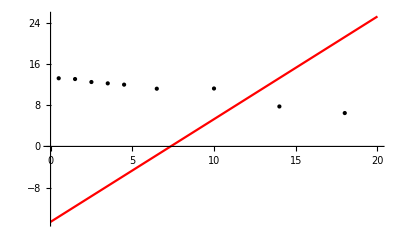

```mathematica
Plot[fiteo[r],{r,0,20},PlotStyle->Red,Epilog:>Point[data]]
```